## Disease Classification

```mathematica
rrules={4201857261303,4201857263490,4201857263409,4201856731968};
```

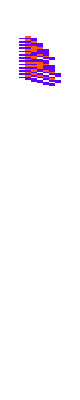
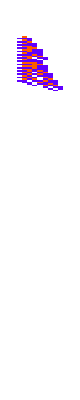
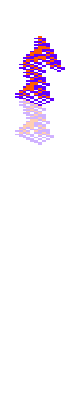
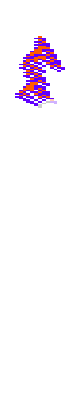
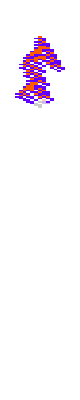
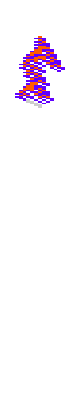
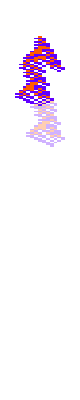
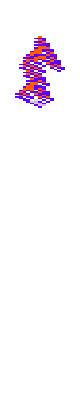
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[SeedRandom[2424+i];PlotDifferences2[CellularAutomaton[{#,3,1},{{1},0},{200,All}],PerturbedCAEvolution[{#,3,1},{{1},0},200,40->1],"Trim"->{2,None}],{i,30}]&/@{4201857261303,4201857263490,4201857263409,4201856731968}
```

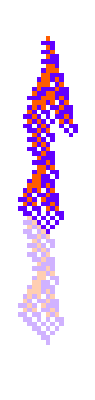
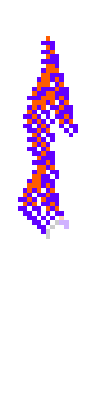
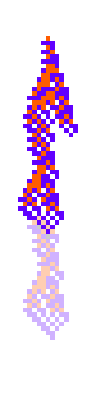
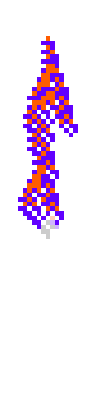
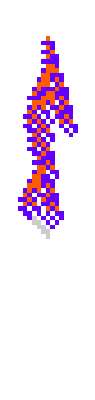
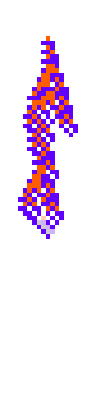
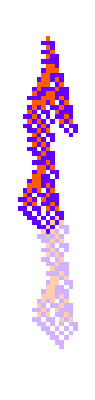
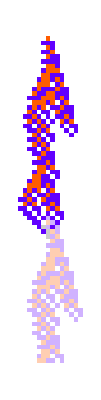
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ru=4201857263409},Table[SeedRandom[2424+i];PlotDifferences2[CellularAutomaton[{ru,3,1},{{1},0},{70,All}],PerturbedCAEvolution[{ru,3,1},{{1},0},70,40->1],"Trim"->{2,None}],{i,30}]]
```

```mathematica
With[{ru=4201857263409},Table[SeedRandom[2424+i];HighlightPerturbations[Reap[PerturbedCAEvolution[{ru,3,1},{{1},0},70,40->1]][[2,1,1]]],{i,30}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ru=4201857263409},Table[SeedRandom[2424+i];PlotDifferences2[CellularAutomaton[{ru,3,1},{{1},0},{70,All}],PerturbedCAEvolution[{ru,3,1},{{1},0},70,20->1],"Trim"->{2,None}],{i,30}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ru=4201857263409},Table[SeedRandom[2424+i];PlotDifferences2[CellularAutomaton[{ru,3,1},{{1},0},{70,All}],PerturbedCAEvolution[{ru,3,1},{{1},0},70,30->1],"Trim"->{2,None}],{i,30}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ru=4201857263409},Table[SeedRandom[2424+i];PlotDifferences2[CellularAutomaton[{ru,3,1},{{1},0},{70,All}],PerturbedCAEvolution[{ru,3,1},{{1},0},70,30->1],"Trim"->{2,None}],{i,50}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[ParallelTable[SeedRandom[546535+i];TestCALifeTime[PerturbedCAEvolution[{4201857263409,3,1},{{1},0},70,30->1]],{i,5000}],{1},PlotRange->{{0,70},Automatic}]
```

-Graphics-

```mathematica
Table[Histogram[ParallelTable[SeedRandom[546535+i];TestCALifeTime[PerturbedCAEvolution[{4201857263409,3,1},{{1},0},70,t->1]],{i,5000}],{1},PlotRange->{{0,70},Automatic},Frame->True],{t,2,50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DistributionChart[Table[ParallelTable[SeedRandom[546535+i];TestCALifeTime[PerturbedCAEvolution[{4201857263409,3,1},{{1},0},70,t->1]],{i,5000}],{t,2,50,5}]]
```

-Graphics-

```mathematica
DistributionChart[Table[ParallelTable[SeedRandom[546535+i];TestCALifeTime[PerturbedCAEvolution[{4201857263409,3,1},{{1},0},70,t->1]],{i,5000}],{t,2,50}]]
```

-Graphics-

#### When it’s stretched to the limit, using all rule elements, it’s more likely fail completely when something is changed

Is that a measure of redundancy?   [I.e. can you use different cell values and get “the same results”]

### When do you see a region of change, with the same pattern all around it?

Once the change is healed across a whole row ... it will stay healed until there’s another perturbation   [ in that case, it’s “masked” the perturbation ]

#### Therapies are like Maxwell’s demons (trying to put Humpty Dumpty together again...)

### If the system is modular, maybe it’s like the Titanic, with “firewalls” in between parts

Does a periodic change in the fitness function lead to modularity?

```mathematica
gens=Keys[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]];
```

```mathematica
gensCallouts={{"[◼]", "quickDepict"}}[{2,2},#,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"][#]]&/@gens;
```

```mathematica
{gensRuleMap,ruleGensMap}={{"[◼]", "MarkovRuleMap"}}[First/@PositionIndex[gens]];
```

```mathematica
size=Length[ruleGensMap];
```

```mathematica
ruleIndex=AssociationThread[Keys[ruleGensMap],Range[size]];
```

```mathematica
gensRuleIndices=Lookup[gensRuleMap,Key@#]&/@gens;
```

(Long computation time + 8 GB)

```mathematica
arMarkovWeights=Parallelize@AssociationMap[{{"[◼]", "FitnessMarkovWeights"}}[{{"[◼]", "arFitness"}}[#]]&,Union[Range[120]/100,Range[600,900]/1000]];
```

```mathematica
arMarkovMatrices=N[#/Total/@#]&/@arMarkovWeights;
```

```mathematica
arfollowing[schedule_]:=With[{arScheduleData=Catenate@FoldList[With[{matrix=arMarkovMatrices[First[#2]]},Rest[NestList[#.matrix&,#1[[-1]],Length[#2]]]]&,{UnitVector[Length[arMarkovMatrices[[1]]],1]},Split[#]]&@schedule},Total/@arScheduleData[[All,Lookup[ruleIndex,#]]]&/@gensRuleIndices]
```

```mathematica
With[{sc=Table[First@Nearest[Union[Range[120]/100,Range[600,900]/1000],1.2t /2500],{t,1,2500}]},
ListLinePlot[MapThread[Which[Max[#1]>.2,With[{x=PositionLargest[#1,1][[1,1]]},Callout[#1,#2,x]],Max[#1]>.1,Callout[#1,#2],True,#1]&,{#2,gensCallouts}],PlotRange->Full,Frame->True,Epilog->Inset[ListStepPlot[#1,PlotStyle->Red,Frame->True],Scaled[{1,.95}],{Right,Top},Scaled[.35{1,1}]]]&[sc,arfollowing[sc]]]
```

```mathematica
ListPlot[Table[First@Nearest[Union[Range[120]/100,Range[600,900]/1000],1.2t /2500],{t,1,2500}]]
```

-Graphics-